# Homework 1

1) Determine the DFT of sequence x(n)=R_4(n) with N=4, N=8 and N=16 by
Matlab, and plot the figures;
2) Determine the FT of sequence x(n)=R_4(n) by Matlab, and plot the figure;
3) Compare figures and give the relationship between DFT and FT;

```mathematica
myDFT[x_?VectorQ,n_?IntegerQ]:=With[{
Wn=Exp[-2π*ⅈ/n]^Table[i*j,{i,0,n-1},{j,0,n-1}],
xn=PadRight[x,n](*不足补零*)
},
Wn.xn(*'.'是点乘*)
]
myDFT[x_?VectorQ]:=myDFT[x,Length[x]]
```

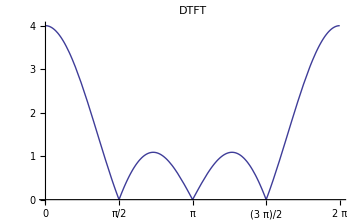
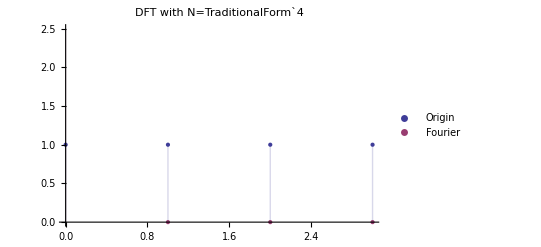
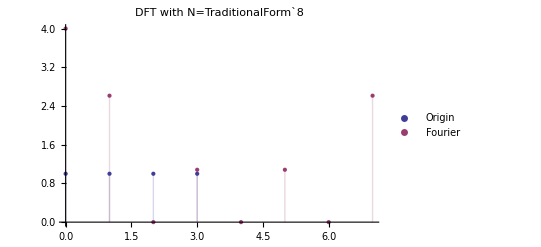
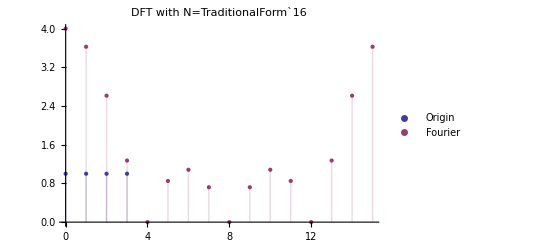
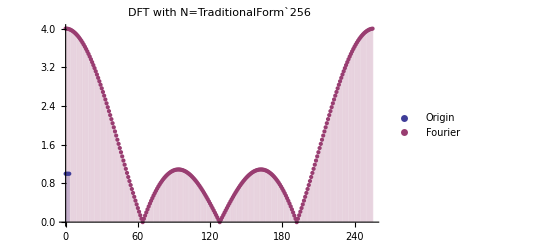
-Graphics- | 
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
With[{n={{4,8},{16,256}}},(*DFT中N的取值*)
Grid[(*栅格布局*)
{{
Plot[
Abs@FourierSequenceTransform[Boole[t≥0&&t<4],t,ω]//Evaluate,
{ω,0,2π},
PlotLabel->"DTFT",
Ticks->{{0,π/2,π,3π/2,2π},Automatic},
ImageSize->Medium
],
SpanFromLeft(*使左侧元素横跨*)
}
}~Join~(*连接DTFT与DFT图像*)
Table[
ListPlot[{
{Range[0,Length[#]-1],#}ᵀ,
{Range[0,n[[i,j]]-1],Abs@myDFT[#,n[[i,j]]]}ᵀ
},
PlotLegends->{"Origin","Fourier"},
PlotLabel->StringForm["DFT with N=`1`",n[[i,j]]],
Filling->Axis
]&@{1,1,1,1},
{i,{1,2}},{j,{1,2}}
],
Alignment->Center,
Frame->All
]
]
```